```mathematica
(*Defining Constants as global variables*)
c = 299792458 (*Speed Of Light*);

(*Eqn numbers correspond to that of the supplementary material*)
```

```mathematica
(*Equation for a Gaussian Photon WavePacket*)
psi[x_,x0_,σ_]:=((1/(2*Pi*(σ^2)))^(1/4))*Exp[(-1/4)*((x-x0)/σ)^2];(*Eqn 1*)

(*Wavepacket Equation for Photon 1 Coming from Ground Station A*)
psi1[x_,x0_,σ_]:=psi[x,0,σ];
(*Wavepacket Equation for Photon 2 Coming from Ground Station B*)
psi2[x_,x0_,σ_]:=psi[x,x0,σ];

(*Notation difference: The path difference in the supplementary material is denoted by Δx, but here we denote it by x0, because we set x0 of psi1 to 0 and x0 of psi2 to x0, therefore the path difference becomes x0-0=x0. Since the origin can be chosen anywhere along the photon paths, the absolute position of the paths don't matter, only the difference does*)

(*integration of |psi1^2|dx and |psi2^2|dx i.e. the probability of the photon passing through the gating window*)(*Eqn 18*)
Pgw1[x0_,σ_,tmin_,tmax_]:= Integrate[Abs[psi1[x,x0,σ]]^2,{x,c*tmin,c*tmax}];
Pgw2[x0_,σ_,tmin_,tmax_]:= Integrate[Abs[psi2[x,x0,σ]]^2,{x,c*tmin,c*tmax}];

(*integration of psi1 times conjugate psi2 *)
γ[x0_,σ_,tmin_,tmax_]:=Abs[Integrate[psi1[x,x0,σ]*psi2[x,x0,σ],{x,c*tmin,c*tmax}]]^2;(*Eqn 16*)

(*Fidelity due to mode mismatch*)
Fic[x0_,σ_,tmin_,tmax_] := (1/2) + γ[x0,σ,tmin,tmax]/(2*Pgw1[x0,σ,tmin,tmax]*Pgw2[x0,σ,tmin,tmax]);(*Eqn 20*)
```

```mathematica
(*Geometries*)

(*Trigonometries i.e. relationships between zenith angles, ground seperations, satellite altitude and position, etc.*)
(*Free Parameters: h, θ1, DG = ground distance*) 
ER = 6.371 * 10^6; (*Earth's Radius in m*)

(*GS = Ground Station*)
(*h is altitude of the satellite*)
(*theta is zenith angle*)
(*alpha is the angle between two lines: the line from the ground station to the earth's centre and the line from the satellite to the earth's centre*)
(*We assume the two ground stations, satellite, and the centre of earth, all are in the same plane*)

(*First GS*)
zθ[h_,θ_] :=Sqrt[h^2 + 2*h*ER + (ER * Cos[θ])^2] -ER * Cos[θ];(*Eqn 21*)
zα[h_,α_]:=Sqrt[ER^2 + (ER + h)^2 -2*ER*(ER+h)*Cos[α]];(*Eqn 23*)
α[h_,θ_]:=ArcCos[(ER + zθ[h,θ]*Cos[θ])/(ER+h)];(*Eqn 24*)
hθ[z_,θ_]:=Sqrt[ER^2+z^2 + 2*z*ER*Cos[θ]]-ER;(*Eqn 22*)

(*Second GS*)
α2[h_,θ1_,DG_]:=(DG/ER)-α[h,θ1];(*Eqn 25*)
θ2[h_,θ1_,DG_]:=ArcCos[((ER+h)*Cos[α2[h,θ1,DG]] - ER)/zα[h,α2[h,θ1,DG]]];(*Rearranging terms from the α[h_,θ_] equation and substituting α2 in place of α to get θ2*)
zθ2[h_,θ1_,DG_]:=zθ[h,θ2[h,θ1,DG]];

(*Zenith Angle θe = θ1 = θ2 for the satellite to be equidistant from both GS*)
θe[h_,DG_]:=ArcCos[((ER+h)*Cos[DG/(2*ER)]-ER)/zα[h,DG/(2*ER)]];(*Eqn 26*)
```

```mathematica
θe[300000,1000000]
```

1.08005

```mathematica
(*Error due to beam widening, beam wandering, pointing errors and tracking errors*)

Cw = 2.2354 * 10^(-12);(*Constant*)

κ0[θ_,λ_]:=(1.46*((2*Pi/λ)^2)*Sec[θ]*Cw)^(-3/5);(*Eqn 28*)

(*Final Beam Width*)
wSquared[w0_,z_,λ_,κ0_] := w0^2(1+(z*λ/(Pi*(w0^2)))^2)+2*((λ*z/(Pi*κ0))^2);(*Eqn 27*)

(*Channel Efficiency*)
ηw[RA_,wSquared_,z_,σtr_]:=1-Exp[-2*(RA^2)/(wSquared+(z*10^(-6))^2 + σtr^2)];(*Eqn 29*)
```

```mathematica
ηw[RA,wSquared[w0,zθ[h,θe[h,DG]],λ,κ0[θe[h,DG],λ]],zθ[h,θe[h,DG]],σtr]
```

0.024329

```mathematica
(*Atmospheric Efficiency*)

α0 = 5*10^(-6);(*at λ=800nm*)
hTilde = 6600;(*in metres*)
ηa[h_,θ_]:=Exp[-α0*NIntegrate[Exp[-hθ[y,θ]/hTilde],{y,0,zθ[h,θ]}]];(*Eqn 30*)
```

```mathematica
(*Overall Single Photon Channel Efficiency*)
(*Eqn 31*)
ηph[RA_,w0_,h_,θ_,λ_,σtr_,ηm_]:= ηw[RA,wSquared[w0,zθ[h,θ],λ,κ0[θ,λ]],zθ[h,θ],σtr]*ηa[h,θ]*ηm;
ηA[RA_,w0_,h_,θ_,λ_,σtr_,ηm_,x0_,σ_,tmin_,tmax_]:=ηph[RA,w0,h,θ,λ,σtr,ηm]*Pgw1[x0,σ,tmin,tmax];
ηB[RA_,w0_,h_,θ2_,λ_,σtr_,ηm_,x0_,σ_,tmin_,tmax_]:=ηph[RA,w0,h,θ2,λ,σtr,ηm]*Pgw2[x0,σ,tmin,tmax];
```

```mathematica
(*Stray Photons*)

EE = 0.3;(*Earth's Albedo*)
IS = 4.61 * 10^27;(*Solar Spectral Irradiance in SI Units*)
M = 0.14;(*Moon Albedo*)
rM = 1737.4*1000;(*Moon's radius in m*)
lME = 363300*1000;(*Earth moon distance in m*)
p = 6.626*10^-34;(*Planck's const*)
kB = 1.381*10^-23;(*Boltzmann's const*)

(*Day Time*)
ND[RA_,θFOV_]:= EE*IS *(RA *θFOV)^2; (*Eqn 32*)

(*Night Time*)
IBB[λ_,T_]:= (2*c/(λ^4))*(1/(Exp[p*c/(λ*kB*T)]-1));(*Eqn 34*)
NN[λ_,T_,RA_,θFOV_]:=Pi*IBB[λ,T]*(RA *θFOV)^2 + ND[RA ,θFOV]*M*(rM/lME)^2;(*Eqn 33*)

(*Stray Photon Rates*)
rday[CD_,h_,θ_,ηm_,RA_,θFOV_,Δλ_]:=CD + (1/2)*ηa[h,θ]*ηm*ND[RA ,θFOV]*Δλ;(*Eqn 35*)
rnight[CD_,h_,θ_,ηm_,RA_,θFOV_,Δλ_,λ_,T_]:=CD + (1/2)*ηa[h,θ]*ηm*NN[λ,T,RA ,θFOV]*Δλ;(*Eqn 35*)

(*(Poissonian) Probability of n stray photons passing through a gating window of duration t*)
Psp[n_,r_,t_]:=((r*t)^n)*Exp[-r*t]/ (n!);(*Eqn 36*)
```

```mathematica
rnight[CD,h,Pi/4,ηm,RA,θFOV,Δλ,800,300]
rday[CD,h,Pi/4,ηm,RA,θFOV,Δλ]
```

1529.72

9.28277×10^6

```mathematica
N[Psp[1,10^7,10^-8]]
```

0.0904837

```mathematica
(*Finally*)

(*Probability of detector click configuration 1010*)
Pm1010[PG0_,PG1_,PG2_,PD0_,PD1_,PD2_]:=PG2*(PD0+2*PD1+PD2)+2*PG1*(PD1+PD2)+PG0*PD2;(*Eqn 37,45*)

(*Overall Dual Channel Efficiency i.e. Success Probability of the Protocol*)
ηtot[PG0_,PG1_,PG2_,PD0_,PD1_,PD2_] := 4*Pm1010[PG0,PG1,PG2,PD0,PD1,PD2];(*Eqn 47*)

(*probability of a legitimate coincidence given the success signature*)
PS[PG0_,PG1_,PG2_,PD0_,PD1_,PD2_]:=PG2*(PD0+2*PD1+PD2)/Pm1010[PG0,PG1,PG2,PD0,PD1,PD2];(*Eqn 48*)

(*Overall Final Fidelity of the swapped state shared between the two ground stations*)
F[PG0_,PG1_,PG2_,PD0_,PD1_,PD2_,x0_,σ_,tmin_,tmax_]:=PS[PG0,PG1,PG2,PD0,PD1,PD2]*Fic[x0,σ,tmin,tmax] + (1-PS[PG0,PG1,PG2,PD0,PD1,PD2])*(1/4); (*Eqn 51*)

(*Eqn 39-41*)
PG0[ηA_,ηB_]:=(1-ηA)*(1-ηB);
PG1[ηA_,ηB_]:= (ηA*(1-ηB)+ηB*(1-ηA))*(1/4) + (1/16)*ηA*ηB;
PG2[ηA_,ηB_]:= (1/8)*ηA*ηB;

(*Eqn 42-44*)
PD0[Psp0_]:=Psp0^4;
PD1[Psp0_]:=(Psp0^3)*(1-Psp0);
PD2[Psp0_]:=(Psp0^2)*(1-Psp0)^2;



(*Substituting the input variables with their respective functions to derive the final formulas*)


(*Daytime*)
ηtotday[RA_,w0_,h_,θ_,θ2_,λ_,σtr_,ηm_,x0_,σ_,tmin_,tmax_,CD_,θFOV_,Δλ_]:=ηtot[PG0[ηA[RA,w0,h,θ,λ,σtr,ηm,x0,σ,tmin,tmax],ηB[RA,w0,h,θ2,λ,σtr,ηm,x0,σ,tmin,tmax]],PG1[ηA[RA,w0,h,θ,λ,σtr,ηm,x0,σ,tmin,tmax],ηB[RA,w0,h,θ2,λ,σtr,ηm,x0,σ,tmin,tmax]],PG2[ηA[RA,w0,h,θ,λ,σtr,ηm,x0,σ,tmin,tmax],ηB[RA,w0,h,θ2,λ,σtr,ηm,x0,σ,tmin,tmax]],PD0[Psp[0,rday[CD,h,θ,ηm,RA,θFOV,Δλ],tmax-tmin]],PD1[Psp[0,rday[CD,h,θ,ηm,RA,θFOV,Δλ],tmax-tmin]],PD2[Psp[0,rday[CD,h,θ,ηm,RA,θFOV,Δλ],tmax-tmin]]];

Fday[RA_,w0_,h_,θ_,θ2_,λ_,σtr_,ηm_,x0_,σ_,tmin_,tmax_,CD_,θFOV_,Δλ_]:=F[PG0[ηA[RA,w0,h,θ,λ,σtr,ηm,x0,σ,tmin,tmax],ηB[RA,w0,h,θ2,λ,σtr,ηm,x0,σ,tmin,tmax]],PG1[ηA[RA,w0,h,θ,λ,σtr,ηm,x0,σ,tmin,tmax],ηB[RA,w0,h,θ2,λ,σtr,ηm,x0,σ,tmin,tmax]],PG2[ηA[RA,w0,h,θ,λ,σtr,ηm,x0,σ,tmin,tmax],ηB[RA,w0,h,θ2,λ,σtr,ηm,x0,σ,tmin,tmax]],PD0[Psp[0,rday[CD,h,θ,ηm,RA,θFOV,Δλ],tmax-tmin]],PD1[Psp[0,rday[CD,h,θ,ηm,RA,θFOV,Δλ],tmax-tmin]],PD2[Psp[0,rday[CD,h,θ,ηm,RA,θFOV,Δλ],tmax-tmin]],x0,σ,tmin,tmax];

(*Night Time*)
ηtotnight[RA_,w0_,h_,θ_,θ2_,λ_,σtr_,ηm_,x0_,σ_,tmin_,tmax_,CD_,θFOV_,Δλ_,T_]:=ηtot[PG0[ηA[RA,w0,h,θ,λ,σtr,ηm,x0,σ,tmin,tmax],ηB[RA,w0,h,θ2,λ,σtr,ηm,x0,σ,tmin,tmax]],PG1[ηA[RA,w0,h,θ,λ,σtr,ηm,x0,σ,tmin,tmax],ηB[RA,w0,h,θ2,λ,σtr,ηm,x0,σ,tmin,tmax]],PG2[ηA[RA,w0,h,θ,λ,σtr,ηm,x0,σ,tmin,tmax],ηB[RA,w0,h,θ2,λ,σtr,ηm,x0,σ,tmin,tmax]],PD0[Psp[0,rnight[CD,h,θ,ηm,RA,θFOV,Δλ,λ,T],tmax-tmin]],PD1[Psp[0,rnight[CD,h,θ,ηm,RA,θFOV,Δλ,λ,T],tmax-tmin]],PD2[Psp[0,rnight[CD,h,θ,ηm,RA,θFOV,Δλ,λ,T],tmax-tmin]]];

Fnight[RA_,w0_,h_,θ_,θ2_,λ_,σtr_,ηm_,x0_,σ_,tmin_,tmax_,CD_,θFOV_,Δλ_,T_]:=F[PG0[ηA[RA,w0,h,θ,λ,σtr,ηm,x0,σ,tmin,tmax],ηB[RA,w0,h,θ2,λ,σtr,ηm,x0,σ,tmin,tmax]],PG1[ηA[RA,w0,h,θ,λ,σtr,ηm,x0,σ,tmin,tmax],ηB[RA,w0,h,θ2,λ,σtr,ηm,x0,σ,tmin,tmax]],PG2[ηA[RA,w0,h,θ,λ,σtr,ηm,x0,σ,tmin,tmax],ηB[RA,w0,h,θ2,λ,σtr,ηm,x0,σ,tmin,tmax]],PD0[Psp[0,rnight[CD,h,θ,ηm,RA,θFOV,Δλ,λ,T],tmax-tmin]],PD1[Psp[0,rnight[CD,h,θ,ηm,RA,θFOV,Δλ,λ,T],tmax-tmin]],PD2[Psp[0,rnight[CD,h,θ,ηm,RA,θFOV,Δλ,λ,T],tmax-tmin]],x0,σ,tmin,tmax];
```

```mathematica
(*Parameter Values. All values in SI units unless stated otherwise*)(*Check Table in the paper*)



CD = 1500; (*Detector Inherent Dark Count Rate*)
h=500 * 10^3; (*Satellite Altitude in m*)
RA = 0.75; (*Radius of aperture of the receiving telescope at the satellite*)
w0 = 0.025;(*Initial Beam Width*)
θFOV=10^-5;(*Field Of View of Receiving Telescope*)
Δλ=10^-9;(*detector/telescope/filter bandwidth*)
λ=8*10^-7;(*wavelength*)
T=300;(*Temperature of the ground stations*)
c=3*10^8;(*Speed of Light*)
DG=100*10^3;(*Ground Station seperation*)
k=2*3.14159/λ;(*wave number, 2pi/lambda*)
ηm=0.25;(*Measurement Apparatus Error*)
σ = 10*10^-9*c; (*Wavepacket width in terms of distance. Divide by c to get the temporal wavepacket width*)
t=40*10^-9;(*Length of the gating window in seconds*)
tmin =-t/2+10*10^(-9) ; (*Gating Window Start*)
tmax =t/2+10*10^(-9);(*Gating Window End*)
x0=c* (3*10^-9);(*Path Difference, time difference times c, here 3 nanoseconds times c*)
σtr = 0.1;(*Tracking error i.e. the standard deviation in satellite position (in metres)*)



(*/.{CD->500,h->500*1000,RA->0.75,w0->0.25,θFOV->10^-5,Δλ->10^-9,λ->8*10^-7,T->300,c->3*10^8,DG->100*10^3,ηm->0.25,σ -> 10*10^-9*c,t->40*10^-9,tmin -> -t/2+10*10^(-9), tmax -> t/2+10*10^(-9), x0 -> c* (3*10^-9), σtr -> 0.1}*)
```

1529.72

```mathematica
With[{CD=1500,h=500*1000,RA=0.75,w0=0.025,θFOV=10^-5,Δλ=10^-9,λ=8*10^-7,T=300,c=3*10^8,DG=1000*10^3,ηm=0.25,σ = 10*10^-9*c,tmin = -(40*10^-9)/2+10*10^(-9), tmax = (40*10^-9)/2+10*10^(-9), x0 = c* (3*10^-9), σtr = 0.1},ηtotnight[RA,w0,h,θe[h,DG],θe[h,DG],λ,σtr,ηm,x0,σ,tmin,tmax,CD,θFOV,Δλ,T]]
```

2.404×10^-6

```mathematica
With[{CD=1500,h=500*1000,RA=0.75,w0=0.025,θFOV=10^-5,Δλ=10^-9,λ=8*10^-7,T=300,c=3*10^8,DG=1000*10^3,ηm=0.25,σ = 10*10^-9*c,tmin = -(40*10^-9)/2+10*10^(-9), tmax = (40*10^-9)/2+10*10^(-9), x0 = c* (3*10^-9), σtr = 0.1},Fnight[RA,w0,h,θe[h,DG],θe[h,DG],λ,σtr,ηm,x0,σ,tmin,tmax,CD,θFOV,Δλ,T]]
```

0.840444

```mathematica
(*F and Subscript[η, tot] vs satellite altitude h for different ground distance seperations Subscript[D, G]*)
```

```mathematica
valuesOfdg={300,600,900,1200,1500};
hRange=Range[200*10^3,1000*10^3,10*10^3];  

data1=With[{CD=1500,RA=0.75,w0=0.025,θFOV=10^-5,Δλ=10^-9,λ=8*10^-7,T=300,c=3*10^8,ηm=0.25,σ = 10*10^-9*c,tmin = -(40*10^-9)/2+10*10^(-9), tmax = (40*10^-9)/2+10*10^(-9), x0 = c* (3*10^-9), σtr = 0.1},Table[{h/1000,Fnight[RA,w0,h,θe[h,DG*1000],θe[h,DG*1000],λ,σtr,ηm,x0,σ,tmin,tmax,CD,θFOV,Δλ,T]},{DG,valuesOfdg},{h,hRange}]];

data2=With[{CD=1500,RA=0.75,w0=0.025,θFOV=10^-5,Δλ=10^-9,λ=8*10^-7,T=300,c=3*10^8,ηm=0.25,σ = 10*10^-9*c,tmin = -(40*10^-9)/2+10*10^(-9), tmax = (40*10^-9)/2+10*10^(-9), x0 = c* (3*10^-9), σtr = 0.1},Table[{h/1000,ηtotnight[RA,w0,h,θe[h,DG*1000],θe[h,DG*1000],λ,σtr,ηm,x0,σ,tmin,tmax,CD,θFOV,Δλ,T]/(10^-6)},{DG,valuesOfdg},{h,hRange}]];

GraphicsColumn[{

Labeled[ListPlot[data1,Joined->True,PlotLegends->("D_G(km)= "<>ToString[#]&/@valuesOfdg ),Frame->True,PlotRange->{{200,Automatic},All}],{"Fidelity","Satellite Altitude (km)"},{Left,Bottom},RotateLabel->True],

Labeled[ListPlot[data2,Joined->True,PlotLegends->("D_G(km)= "<>ToString[#]&/@valuesOfdg ),Frame->True,PlotRange->{{200,Automatic},Automatic}],{"Success Probability (in units of 10^-6)","Satellite Altitude (km)"},{Left,Bottom},RotateLabel->True],

Labeled[ListPlot[data2,Joined->True,PlotLegends->("D_G(km)= "<>ToString[#]&/@valuesOfdg ),Frame->True,PlotRange->{{200,Automatic},All}],{"Success Probability (in units of 10^-6)","Satellite Altitude (km)"},{Left,Bottom},RotateLabel->True]

},ImageSize->340,Spacings->-20]
```

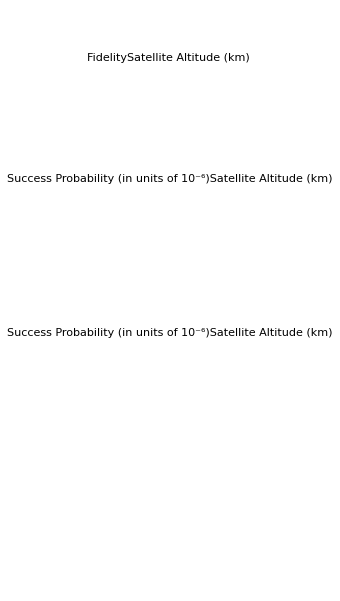

```mathematica
(*F and Subscript[η, tot] vs gating window for different wavepacket thicknesses Subscript[σ, t]*)
```

```mathematica
valuesOfsigma={10,20,30,40};
tRange=Range[1,250,6];  

data1 = With[{CD=1500,h=500*1000,RA=0.75,w0=0.025,θFOV=10^-5,Δλ=10^-9,λ=8*10^-7,T=300,c=3*10^8,DG=1000*10^3,ηm=0.25, x0 = c* (3*10^-9), σtr = 0.1},Table[{t,Fnight[RA,w0,h,θe[h,DG],θe[h,DG],λ,σtr,ηm,x0,σ*10^-9*c,-t*(10^-9)/2,t*(10^-9)/2,CD,θFOV,Δλ,T]},{σ,valuesOfsigma},{t,tRange}]];

data2=With[{CD=1500,h=500*1000,RA=0.75,w0=0.025,θFOV=10^-5,Δλ=10^-9,λ=8*10^-7,T=300,c=3*10^8,DG=1000*10^3,ηm=0.25, x0 = c* (3*10^-9), σtr = 0.1},Table[{t,ηtotnight[RA,w0,h,θe[h,DG],θe[h,DG],λ,σtr,ηm,x0,σ*10^-9*c,-t*(10^-9)/2,t*(10^-9)/2,CD,θFOV,Δλ,T]/(10^-6)},{σ,valuesOfsigma},{t,tRange}]];

GraphicsColumn[{

Labeled[ListPlot[data1,Joined->True,PlotLegends->("σ_t(ns)= "<>ToString[#]&/@valuesOfsigma ),Frame->True],{"Fidelity","Gating Window (ns)"},{Left,Bottom},RotateLabel->True],

Labeled[ListPlot[data2,Joined->True,PlotLegends->("σ_t(ns)= "<>ToString[#]&/@valuesOfsigma ),Frame->True],{"Success Probability(in units of 10^-6)","Gating Window (ns)"},{Left,Bottom},RotateLabel->True]

},ImageSize->300,Spacings->-20]
```

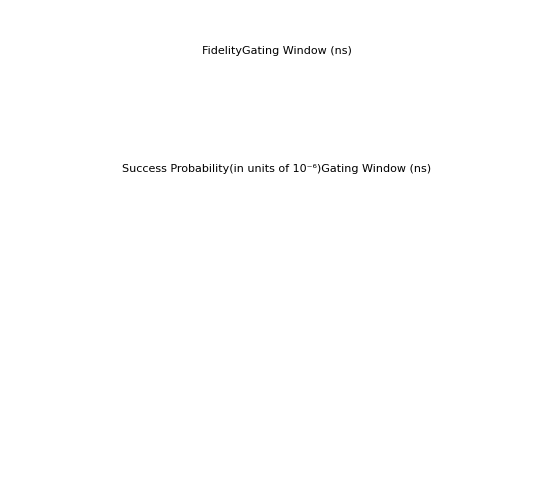

```mathematica
(*Everything except mode mismatch is switched off*)
```

```mathematica
Plot3D[With[{x0 = c* (3*10^-9)},0.5*Pgw1[x0,σ,-(t+10^-8)/2,(t+10^-8)/2]*Pgw1[x0,σ,-(t+10^-8)/2,(t+10^-8)/2]],{σ,(10*10^-9)*c,(100*10^-9)*c},{t,2*10^-9,100*10^-9},AxesLabel->{"Wavepacket width (m)","Gating window (s)","Success Prob"}]
```

-Graphics3D-

```mathematica
Plot3D[With[{x0 = c* (3*10^-9)},Fic[x0,σ,-(t+10^-8)/2,(t+10^-8)/2]],{σ,(10*10^-9)*c,(40*10^-9)*c},{t,2*10^-9,100*10^-9},AxesLabel->{"Wavepacket width (m)","Gating window (s)","Fic"}]
```

-Graphics3D-

```mathematica
(*Scenario where everything except ηw are switched off*)
```

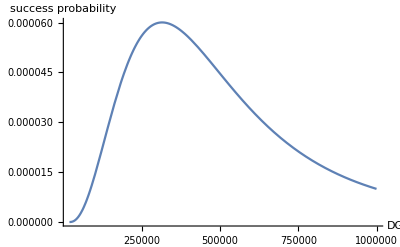

```mathematica
(*{w0,0,10},AxesLabel->{"initial width","success probability"}*)
(*{h,200*1000,1200*1000},AxesLabel->{"Satellite Altitude","success probability"}*)
(*{DG,200*1000,1000*1000},AxesLabel->{"Distance Between Ground Stations","success probability"}*)

ηtotFunction[h_,w0_,RA_,DG_,λ_,σtr_]:=ηtot[PG0[ηw[RA,wSquared[w0,zθ[h,θe[h,DG]],λ,κ0[θe[h,DG],λ]],zθ[h,θe[h,DG]],σtr],ηw[RA,wSquared[w0,zθ[h,θe[h,DG]],λ,κ0[θe[h,DG],λ]],zθ[h,θe[h,DG]],σtr]],PG1[ηw[RA,wSquared[w0,zθ[h,θe[h,DG]],λ,κ0[θe[h,DG],λ]],zθ[h,θe[h,DG]],σtr],ηw[RA,wSquared[w0,zθ[h,θe[h,DG]],λ,κ0[θe[h,DG],λ]],zθ[h,θe[h,DG]],σtr]],PG2[ηw[RA,wSquared[w0,zθ[h,θe[h,DG]],λ,κ0[θe[h,DG],λ]],zθ[h,θe[h,DG]],σtr],ηw[RA,wSquared[w0,zθ[h,θe[h,DG]],λ,κ0[θe[h,DG],λ]],zθ[h,θe[h,DG]],σtr]],1,0,0]

(*Plot for different h values*)
Plot[With[{DG=1000000,RA=0.75,w0=0.025,λ=800*10^-9,σtr=0.1},ηtotFunction[h,w0,RA,DG,λ,σtr]],{h,0,1000000},AxesLabel->{"DG","success probability"},PlotRange->All]
```

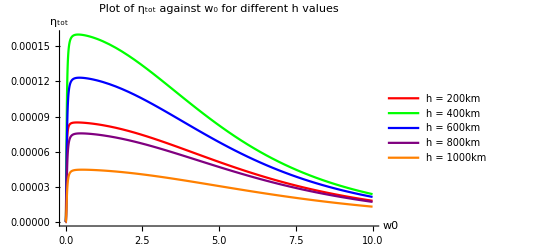

```mathematica
(*Define a list of colors*)colors={Red,Green,Blue,Purple,Orange};

(*Generate individual plots for each h value,each with a corresponding color*)
plotList=MapIndexed[Function[{h,index},Plot[With[{RA=0.75,DG=1000000,λ=800*10^-9,σtr=0.1},ηtotFunction[h,w0,RA,DG,λ,σtr]],{w0,0,10},PlotRange->All,PlotStyle->colors[[First@index]] (*Use the index of h to pick a color*)]],{200000,400000,600000,800000,1000000} (*List of h values*)];

(*Use Show to combine the plots,without PlotLegends option here*)combinedPlot=Show[plotList,PlotRange->All,AxesLabel->{"w0","η_tot"},PlotLabel->"Plot of η_tot against w_0 for different h values"];

(*Manually add a legend using Legended*)
Legended[combinedPlot,Placed[LineLegend[colors,{"h = 200km","h = 400km","h = 600km","h = 800km","h = 1000km"},LegendLayout->"Column"],Right]]
```

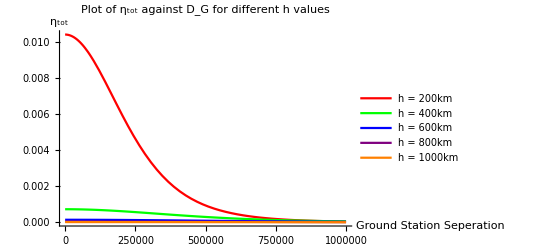

```mathematica
(*Define a list of colors*)colors={Red,Green,Blue,Purple,Orange};

(*Generate individual plots for each h value,each with a corresponding color*)
plotList=MapIndexed[Function[{h,index},Plot[With[{RA=0.75,w0=0.025,λ=800*10^-9,σtr=0.1},ηtotFunction[h,w0,RA,DG,λ,σtr]],{DG,0,1000000},PlotRange->All,PlotStyle->colors[[First@index]] (*Use the index of h to pick a color*)]],{200000,400000,600000,800000,1000000} (*List of h values*)];

(*Use Show to combine the plots,without PlotLegends option here*)combinedPlot=Show[plotList,PlotRange->All,AxesLabel->{"Ground Station Seperation","η_tot"},PlotLabel->"Plot of η_tot against D_G for different h values"];

(*Manually add a legend using Legended*)
Legended[combinedPlot,Placed[LineLegend[colors,{"h = 200km","h = 400km","h = 600km","h = 800km","h = 1000km"},LegendLayout->"Column"],Right]]
```

```mathematica
(*Scenario where everything except ηa is switched off*)
```

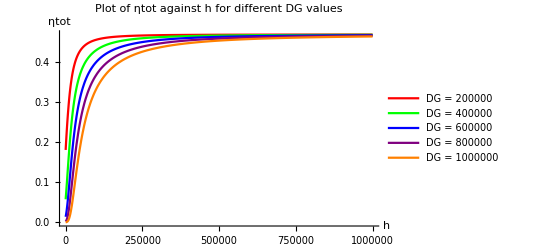

```mathematica
(*Define the main function with placeholders for h and DG*)ηtotFunction[h_,DG_]:=ηtot[PG0[ηa[h,θe[h,DG]],ηa[h,θe[h,DG]]],PG1[ηa[h,θe[h,DG]],ηa[h,θe[h,DG]]],PG2[ηa[h,θe[h,DG]],ηa[h,θe[h,DG]]],1,0,0];

(*Define a list of colors*)
colors={Red,Green,Blue,Purple,Orange};

(*Generate individual plots for each DG value*)
plotList=MapIndexed[Function[{DG,index},Plot[ηtotFunction[h,DG],{h,0,1000000},PlotRange->All,PlotStyle->colors[[First@index]],PlotPoints->50 (*Increase PlotPoints for better resolution if necessary*)]],{200000,400000,600000,800000,1000000} (*List of DG values*)];

(*Combine the plots and manually add a legend*)
Legended[Show[plotList,PlotRange->All,AxesLabel->{"h","ηtot"},PlotLabel->"Plot of ηtot against h for different DG values"],Placed[LineLegend[colors,{"DG = 200000","DG = 400000","DG = 600000","DG = 800000","DG = 1000000"},LegendLayout->"Column"],Right]]
```

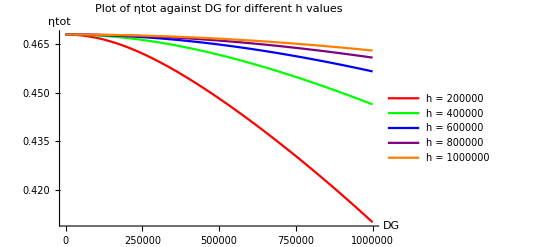

```mathematica
(*Define the main function with placeholders for DG and specific h values*)ηtotFunction[DG_,h_]:=ηtot[PG0[ηa[h,θe[h,DG]],ηa[h,θe[h,DG]]],PG1[ηa[h,θe[h,DG]],ηa[h,θe[h,DG]]],PG2[ηa[h,θe[h,DG]],ηa[h,θe[h,DG]]],1,0,0];

(*Define a list of colors*)
colors={Red,Green,Blue,Purple,Orange};

(*Generate individual plots for each specified h value across the DG range*)
plotList=MapIndexed[Function[{h,index},Plot[ηtotFunction[DG,h],{DG,0,1000000},PlotRange->All,PlotStyle->colors[[First@index]],PlotPoints->50 (*May need to adjust for better resolution*)]],{200000,400000,600000,800000,1000000} (*List of h values*)];

(*Combine the plots and manually add a legend*)
Legended[Show[plotList,PlotRange->All,AxesLabel->{"DG","ηtot"},PlotLabel->"Plot of ηtot against DG for different h values"],Placed[LineLegend[colors,{"h = 200000","h = 400000","h = 600000","h = 800000","h = 1000000"},LegendLayout->"Column"],Right]]
```

```mathematica
(*Everything else except stray photons are switched off*)
```

```mathematica
With[{CD=1500,h=500000,DG=1000000,ηm=0.25,RA=0.75,θFOV=10^-5,Δλ=10^-9,λ=800*10^-9,T=300,t=40*10^-9},ηtot[1,0,0,PD0[Psp[0,rnight[CD,h,θe[h,DG],ηm,RA,θFOV,Δλ,λ,T],t]],PD1[Psp[0,rnight[CD,h,θe[h,DG],ηm,RA,θFOV,Δλ,λ,T],t]],PD2[Psp[0,rnight[CD,h,θe[h,DG],ηm,RA,θFOV,Δλ,λ,T],t]]]]
```

1.49717×10^-8

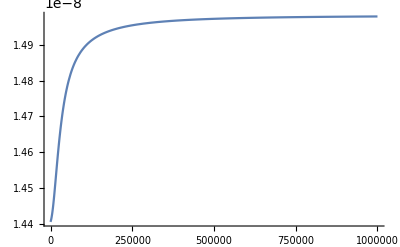

```mathematica
Plot[With[{CD=1500,DG=1000000,ηm=0.25,RA=0.75,θFOV=10^-5,Δλ=10^-9,λ=800*10^-9,T=300,t=40*10^-9},ηtot[1,0,0,PD0[Psp[0,rnight[CD,h,θe[h,DG],ηm,RA,θFOV,Δλ,λ,T],t]],PD1[Psp[0,rnight[CD,h,θe[h,DG],ηm,RA,θFOV,Δλ,λ,T],t]],PD2[Psp[0,rnight[CD,h,θe[h,DG],ηm,RA,θFOV,Δλ,λ,T],t]]]],{h,0,1000000},PlotRange->All]
```

```mathematica
With[{CD=1500,h=500000,DG=1000000,ηm=0.25,RA=0.75,θFOV=10^-5,Δλ=10^-9,λ=800*10^-9,T=300,tmin = -(40*10^-9)/2+10*10^(-9), tmax = (40*10^-9)/2+10*10^(-9)},Psp[0,rnight[CD,h,θe[h,DG],ηm,RA,θFOV,Δλ,λ,T],tmax-tmin]]
```

0.999939

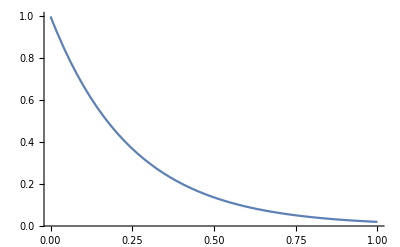

```mathematica
Plot[With[{h=500000,DG=1000000,ηm=0.25,RA=0.75,θFOV=10^-5,Δλ=10^-9,λ=800*10^-9,T=300,tmin = -(40*10^-9)/2+10*10^(-9), tmax = (40*10^-9)/2+10*10^(-9)},Psp[0,rnight[CD,h,θe[h,DG],ηm,RA,θFOV,Δλ,λ,T],tmax-tmin]],{CD,0,100000000},PlotRange->All]
```

```mathematica
(*All sections below this are for Peter's Reference; to be deleted later*)
```

```mathematica
(**)
(**)
(**)
```

```mathematica
(*Analytical Form of the Fidelity and Success Probability*)
```

```mathematica
ηtot[PG0[ηwA*ηaA*ηmA*Pgw1,ηwB*ηaB*ηmB*Pgw2],PG1[ηwA*ηaA*ηmA*Pgw1,ηwB*ηaB*ηmB*Pgw2],PG2[ηwA*ηaA*ηmA*Pgw1,ηwB*ηaB*ηmB*Pgw2],PD0[Psp0],PD1[Psp0],PD2[Psp0]]
```

4 (1/8 Pgw1 Pgw2 ((1-Psp0)^2 Psp0^2+2 (1-Psp0) Psp0^3+Psp0^4) ηaA ηaB ηmA ηmB ηwA ηwB+(1-Psp0)^2 Psp0^2 (1-Pgw1 ηaA ηmA ηwA) (1-Pgw2 ηaB ηmB ηwB)+2 ((1-Psp0)^2 Psp0^2+(1-Psp0) Psp0^3) (1/16 Pgw1 Pgw2 ηaA ηaB ηmA ηmB ηwA ηwB+1/4 (Pgw2 ηaB ηmB (1-Pgw1 ηaA ηmA ηwA) ηwB+Pgw1 ηaA ηmA ηwA (1-Pgw2 ηaB ηmB ηwB))))

```mathematica
Simplify[%119]
```

Psp0^2 (-2+Pgw1 ηaA ηmA ηwA) (-2+Pgw2 ηaB ηmB ηwB)+4 Psp0^4 (-1+Pgw1 ηaA ηmA ηwA) (-1+Pgw2 ηaB ηmB ηwB)-1/2 Psp0^3 (-4+3 Pgw1 ηaA ηmA ηwA) (-4+3 Pgw2 ηaB ηmB ηwB)

```mathematica
F2[PG0_,PG1_,PG2_,PD0_,PD1_,PD2_,γ_,Pgw1_,Pgw2_]:=PS[PG0,PG1,PG2,PD0,PD1,PD2]*(0.5+0.5*(γ/(Pgw1*Pgw2))) + (1-PS[PG0,PG1,PG2,PD0,PD1,PD2])*(1/4);
F2[PG0[ηwA*ηaA*ηmA*Pgw1,ηwB*ηaB*ηmB*Pgw2],PG1[ηwA*ηaA*ηmA*Pgw1,ηwB*ηaB*ηmB*Pgw2],PG2[ηwA*ηaA*ηmA*Pgw1,ηwB*ηaB*ηmB*Pgw2],PD0[Psp0],PD1[Psp0],PD2[Psp0],γ,Pgw1,Pgw2]
```

(Pgw1 Pgw2 ((1-Psp0)^2 Psp0^2+2 (1-Psp0) Psp0^3+Psp0^4) (0.5+(0.5 γ)/(Pgw1 Pgw2)) ηaA ηaB ηmA ηmB ηwA ηwB)/(8 (1/8 Pgw1 Pgw2 ((1-Psp0)^2 Psp0^2+2 (1-Psp0) Psp0^3+Psp0^4) ηaA ηaB ηmA ηmB ηwA ηwB+(1-Psp0)^2 Psp0^2 (1-Pgw1 ηaA ηmA ηwA) (1-Pgw2 ηaB ηmB ηwB)+2 ((1-Psp0)^2 Psp0^2+(1-Psp0) Psp0^3) (1/16 Pgw1 Pgw2 ηaA ηaB ηmA ηmB ηwA ηwB+1/4 (Pgw2 ηaB ηmB (1-Pgw1 ηaA ηmA ηwA) ηwB+Pgw1 ηaA ηmA ηwA (1-Pgw2 ηaB ηmB ηwB)))))+1/4 (1-(Pgw1 Pgw2 ((1-Psp0)^2 Psp0^2+2 (1-Psp0) Psp0^3+Psp0^4) ηaA ηaB ηmA ηmB ηwA ηwB)/(8 (1/8 Pgw1 Pgw2 ((1-Psp0)^2 Psp0^2+2 (1-Psp0) Psp0^3+Psp0^4) ηaA ηaB ηmA ηmB ηwA ηwB+(1-Psp0)^2 Psp0^2 (1-Pgw1 ηaA ηmA ηwA) (1-Pgw2 ηaB ηmB ηwB)+2 ((1-Psp0)^2 Psp0^2+(1-Psp0) Psp0^3) (1/16 Pgw1 Pgw2 ηaA ηaB ηmA ηmB ηwA ηwB+1/4 (Pgw2 ηaB ηmB (1-Pgw1 ηaA ηmA ηwA) ηwB+Pgw1 ηaA ηmA ηwA (1-Pgw2 ηaB ηmB ηwB))))))

```mathematica
Simplify[%122]
```

(0.25-0.125 Pgw2 ηaB ηmB ηwB+0.0625 γ ηaA ηaB ηmA ηmB ηwA ηwB+Pgw1 ηaA ηmA ηwA (-0.125+0.09375 Pgw2 ηaB ηmB ηwB)+Psp0 (-0.5+0.375 Pgw2 ηaB ηmB ηwB+Pgw1 ηaA ηmA ηwA (0.375-0.28125 Pgw2 ηaB ηmB ηwB))+Psp0^2 (0.25-0.25 Pgw2 ηaB ηmB ηwB+Pgw1 ηaA ηmA ηwA (-0.25+0.25 Pgw2 ηaB ηmB ηwB)))/(1.-0.5 Pgw2 ηaB ηmB ηwB+Pgw1 ηaA ηmA ηwA (-0.5+0.25 Pgw2 ηaB ηmB ηwB)+Psp0 (-2.+1.5 Pgw2 ηaB ηmB ηwB+Pgw1 ηaA ηmA ηwA (1.5-1.125 Pgw2 ηaB ηmB ηwB))+Psp0^2 (1.-1. Pgw2 ηaB ηmB ηwB+Pgw1 ηaA ηmA ηwA (-1.+1. Pgw2 ηaB ηmB ηwB)))

```mathematica
(*Beam Widening/Wandering vs Mode Mismatch*)
```

```mathematica
With[{w0=0.025,h=500000,DG=1000000,λ=800*10^-9},(Sqrt[wSquared[w0,zθ[h,θe[h,DG]],λ,κ0[θe[h,DG],λ]]+(zθ[h,θe[h,DG]])^2]-zθ[h,θe[h,DG]])/c]
```

2.7284×10^-13

```mathematica
(*The path difference between the longest possible path (Along the edge of the conical beam i.e. sqrt[w^2+z^2]) and the shortest possible path (along the centre of the conical beam i.e. z) of a photon is 1/10th of a picosecond, which is far lower than the nanosecond scales we are considering for our path difference between the two ground photons. Therefore, we can consider beam widening/wandering and mode-mismatch as independent effects*)
```